```mathematica
Clear[en];en[ξ_,ηx_,kxsc_,n_,sign_,rat_,Bsc_]=kxsc ηx+sign/8 √(((Bsc rat+Abs[Bsc]+2 n Abs[Bsc]) (64+96 kxsc-16 kxsc^2 (-1+ξ) ξ+(6+kxsc ξ)^2 (Bsc+((1+2 n) Abs[Bsc])/rat)))/rat);
(* Plotting 8 a0  energy/vx versus a0 Kx, expressing with the help of Bsc = B a0^2*)
```

-0.131479

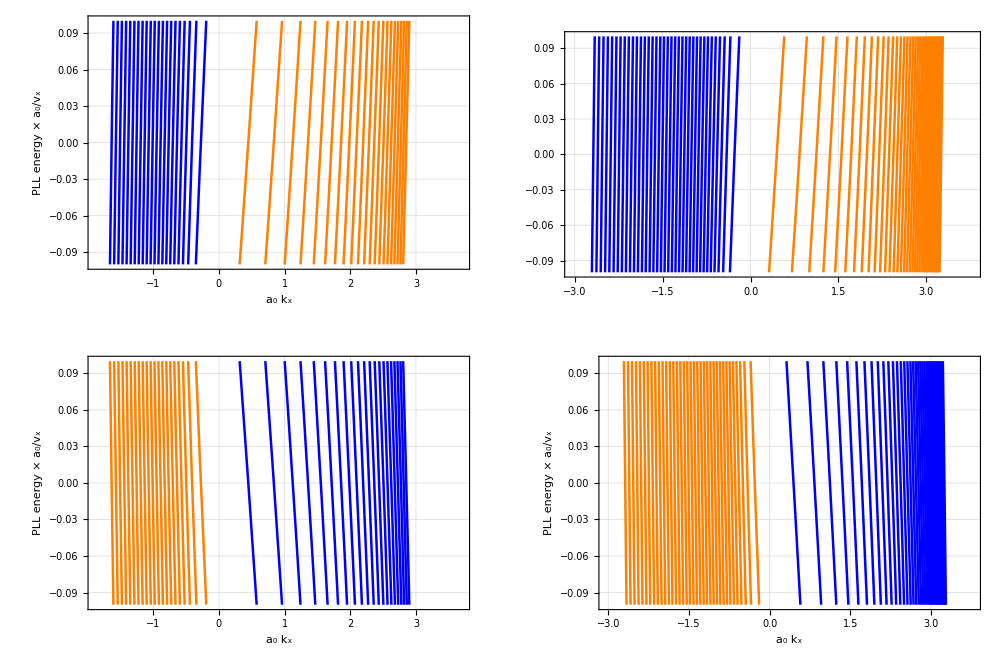

```mathematica
Bval=1*10^(-2); lim=20;limen=0.1;
 rati=1/9;
styles={Directive[Orange,Thickness[0.004]],Directive[Blue,Thickness[0.004]]};
(**************)
 etaval =  0.9;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,rati,Bval];


(* valley D*)
p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,20}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->{-limen,limen},Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}](* {{left,right},{bottom,top}}*)

Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,rati,Bval];


(* valley D'*)
p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,35}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->{-limen,limen},Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}]


uplim=4;
s1=Show[{p1[1,{2,uplim}],p1[-1,{2,uplim}]}];
s2=Show[{p2[1,{3.5,uplim}],p2[-1,{3.5,uplim}]}];
(* for negative ηx *)
(**************)
 etaval = -etaval;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,rati,Bval];


p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,ni,sign],{ni,0,20}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->{-limen,limen},Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}];

Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]


p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,35}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->{-limen,limen},Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}];


uplim=4;
s11=Show[{p1[1,{2,uplim}],p1[-1,{2,uplim}]}];
s12=Show[{p2[1,{3.5,uplim}],p2[-1,{3.5,uplim}]}];
allpl=GraphicsGrid[{{s1,s2},{s11,s12}},Spacings->{20,20},ImageSize->1000]
```

-0.160807

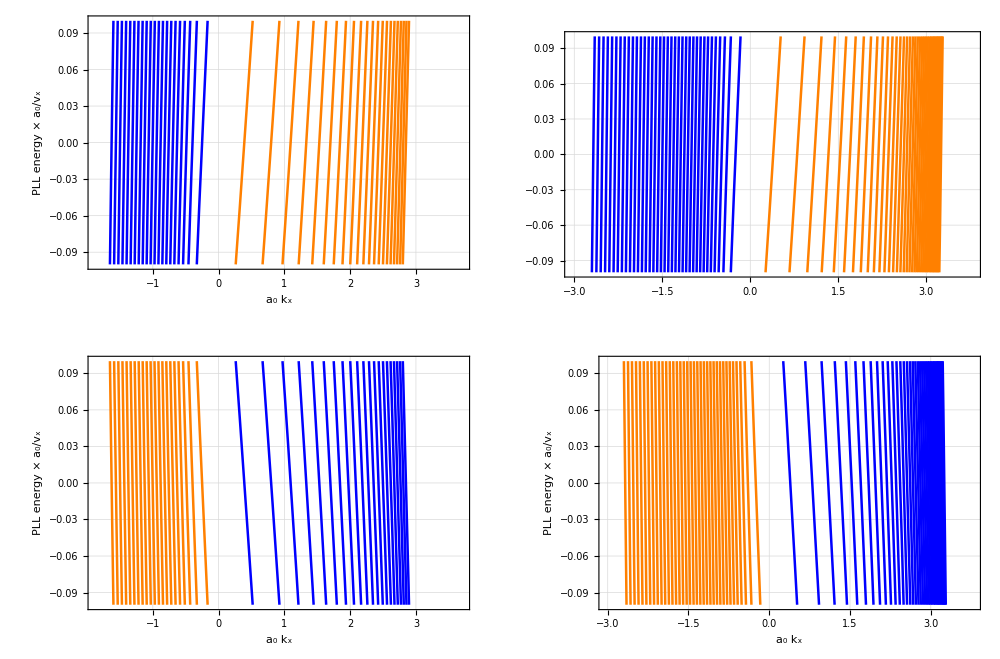

```mathematica
Bval=-1*10^(-2); lim=20;limen=0.1;
 rati=1/9;
styles={Directive[Orange,Thickness[0.004]],Directive[Blue,Thickness[0.004]]};
(**************)
 etaval =  0.9;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,rati,Bval];


(* valley D*)
p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,20}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->{-limen,limen},Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}](* {{left,right},{bottom,top}}*)

Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,rati,Bval];


(* valley D'*)
p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,35}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->{-limen,limen},Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}]


uplim=4;
s1=Show[{p1[1,{2,uplim}],p1[-1,{2,uplim}]}];
s2=Show[{p2[1,{3.5,uplim}],p2[-1,{3.5,uplim}]}];
(* for negative ηx *)
(**************)
 etaval = -etaval;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,rati,Bval];


p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,ni,sign],{ni,0,20}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->{-limen,limen},Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}];

Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]


p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,35}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->{-limen,limen},Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}];


uplim=4;
s11=Show[{p1[1,{2,uplim}],p1[-1,{2,uplim}]}];
s12=Show[{p2[1,{3.5,uplim}],p2[-1,{3.5,uplim}]}];
allpl=GraphicsGrid[{{s1,s2},{s11,s12}},Spacings->{20,20},ImageSize->1000]
```